# SWAP - improved

## Noiseless cases

## Just the coupling, no valley effects

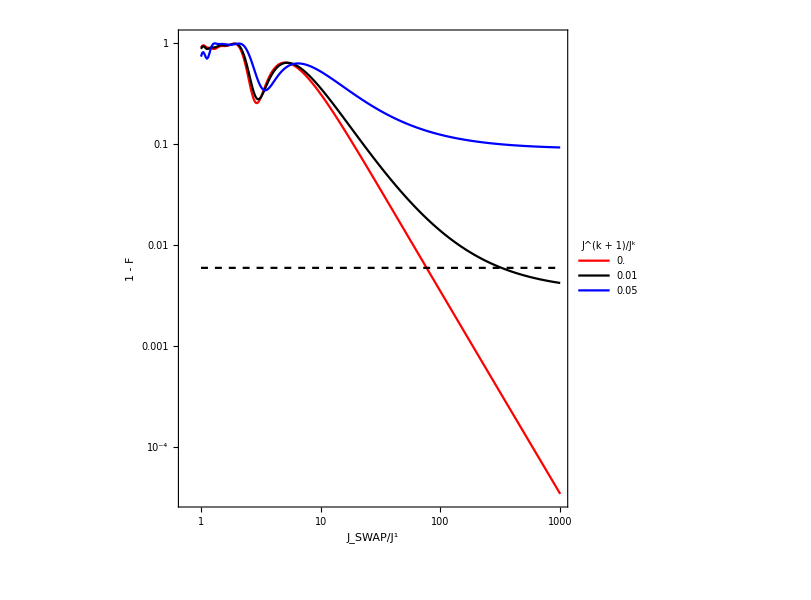

```mathematica
SetDirectory[NotebookDirectory[]];
allTogether = True;
plotdata = {};
plots = {};
stringσJs = {};
Do[
length = l;
singlet = sing;
β = beta;
β2= beta;
σJ = 0.0;
σγ = 0.0;
στ = 0.0;
spacing = If[σJ == 0, 0.01, 0.02];
nReals=10000;
nRealsPrime= If[σJ == 0, 0,nReals];
disGam=dg;
filename = "jdata/"<>ToString[length]<>"_"<>If[singlet,"s","up"]<>"_β"<>StringPadRight[ToString[β2],4,"0"]<>"_γ"<>StringPadRight[ToString[disGam],4,"0"]<>"_"<>"σJ"<>StringPadRight[ToString[N[σJ]],4,"0"]<>"_"<>"σγ"<>StringPadRight[ToString[N[σγ]],4,"0"]<>"_"<>"στ"<>StringPadRight[ToString[N[στ]],4,"0"]<>"_"<>StringPadLeft[ToString[nRealsPrime],5,"0"]<>"_"<>ToString[spacing]<>".m";
If[FileExistsQ[filename],
	AppendTo[stringσJs,ToString[beta]];
	data = Import[filename];
	If[allTogether,
		AppendTo[plotdata,data];
	,
		AppendTo[plots,ListLogLogPlot[data,Joined->True,AspectRatio->1,ImageSize->Medium,Frame->True,PlotLabel->"L = "<>ToString[length]<>", β = "<>ToString[β]<>", β2="<>ToString[β20],PlotRange->{0,1}]]
	]
]

,{l,{6}},{beta,{0.00,0.01,0.05}},{dg,{0.0}},{sing,{False}}];

ECThreshold=1-0.999^(2(leng-1));
NicholF=1-0.9^(2(leng-1));
PettaF=1-0.84^(2(leng-1));
If[allTogether,
	finalplot = Show[ListLogLogPlot[plotdata,Joined->True,AspectRatio->1,ImageSize->600,Frame->True,LabelStyle->20,FrameLabel->{"J_SWAP/J^1","1 - F"},PlotRange->{1*10^-4.5,1.1}(*,PlotLabel->"L = "<>ToString[length]<>".   Δ>>1 meV"*),PlotStyle->{Red,Black,Blue},PlotLegends->LineLegend[Automatic, stringσJs, LegendFunction -> Framed, LegendLabel -> "J^(k + 1)/J^k",LabelStyle->20]],LogLogPlot[{(*PettaF,NicholF,*)ECThreshold},{x,1,1000},PlotStyle->{(*{Dashed,Red},*){Dashed,Black}(*,{Dashed,Blue}*)}]]
,
	Row[plots,Spacer[110]]
]
```

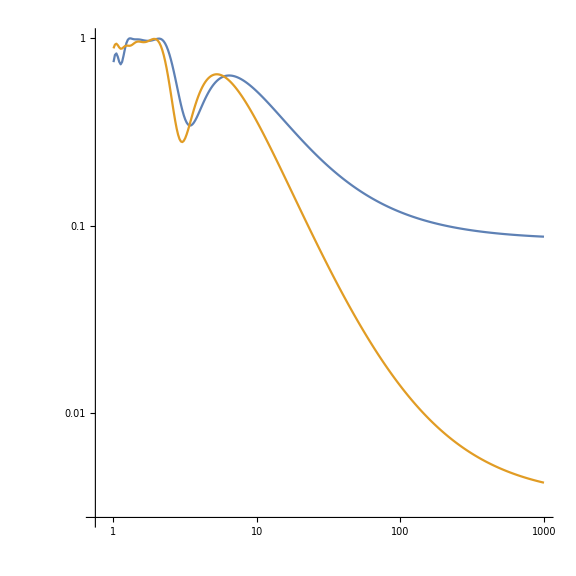

```mathematica
SetDirectory[NotebookDirectory[]];
Clear[file1,file2];
file1 = "data/newFunction/6_up_0.05_γ=0__0.01__σJ=0.";
file2 = "jdata/6_up_β0.01_γ0.00_σJ0.00_σγ0.00_στ0.00_00000_0.01.m";
data1 =( <<(filename));
data2 = Import[file2];
ListLogLogPlot[{data1,data2},Joined->True,AspectRatio->1,ImageSize->Large]
```

```mathematica
Max[Abs[data1-data2]]
```

0.000452824

```mathematica
Export["couplingeffects.pdf",finalplot]
```

couplingeffects.pdf

## Just the valleys, no long-range coupling

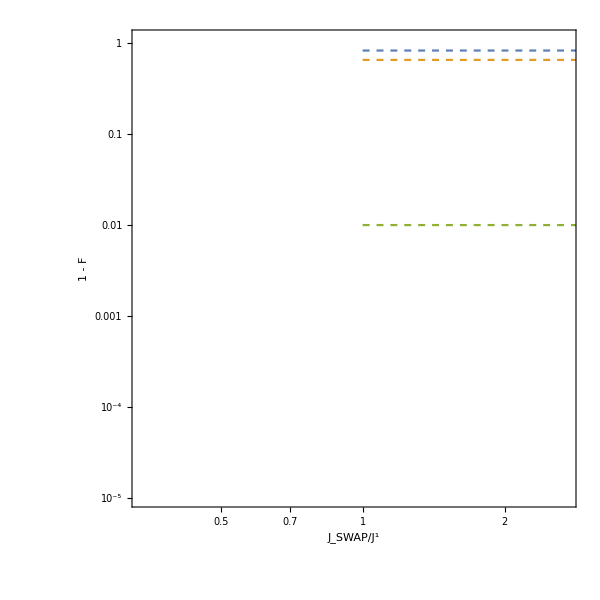

```mathematica
GAMMA = 6.796381511118120480641144794583*10^-5;
SetDirectory[NotebookDirectory[]];
allTogether = True;
plotdata = {};
plots = {};
stringσJs = {};
Do[
leng = l;
singlet = sing;
β = beta;
β2 = beta;
γ0 = If[β==0,0,GAMMA];
σJ = 0.0;
σγ = 0.0;
στ = 0.0;
spacing = If[σJ == 0, 0.01, 0.02];
nReals=10000;
nRealsPrime= If[σJ == 0, 0,nReals];
disGam=dg;
filename = "jdata/"<>ToString[length]<>"_"<>If[singlet,"s","up"]<>"_β"<>StringPadRight[ToString[β2],4,"0"]<>"_γ"<>StringPadRight[ToString[disGam],4,"0"]<>"_"<>"σJ"<>StringPadRight[ToString[N[σJ]],4,"0"]<>"_"<>"σγ"<>StringPadRight[ToString[N[σγ]],4,"0"]<>"_"<>"στ"<>StringPadRight[ToString[N[στ]],4,"0"]<>"_"<>StringPadLeft[ToString[nRealsPrime],5,"0"]<>"_"<>ToString[spacing]<>".m";
If[FileExistsQ[filename],
	AppendTo[stringσJs,StringPadRight[ToString[disGam],4,"0"]];
	data = Import[filename];
	If[allTogether,
		AppendTo[plotdata,data];
	,
		AppendTo[plots,ListLogLogPlot[data,Joined->True,AspectRatio->1,ImageSize->Medium,Frame->True,PlotLabel->"L = "<>ToString[length]<>", β = "<>ToString[β]<>", β2="<>ToString[β20],PlotRange->{0,1}]]
	]
]

,{l,{6}},{beta,{0.0}},{dg,{0.0,0.01,0.05}},{sing,{False}}];

ECThreshold=1-0.999^(2(leng-1));
NicholF=1-0.9^(2(leng-1));
PettaF=1-0.84^(2(leng-1));
If[allTogether,
	Show[ListLogLogPlot[plotdata,Joined->True,AspectRatio->1,ImageSize->600,Frame->True,LabelStyle->20,FrameLabel->{"J_SWAP/J^1","1 - F"},PlotRange->{10*^-6,1.1},PlotLegends->LineLegend[Automatic, stringσJs, LegendFunction -> Framed, LegendLabel -> "γ/J^1",LabelStyle->20]],LogLogPlot[{PettaF,NicholF,ECThreshold},{x,1,1000},PlotStyle->Dashed]]
,
	Row[plots,Spacer[110]]
]
```

## Both!

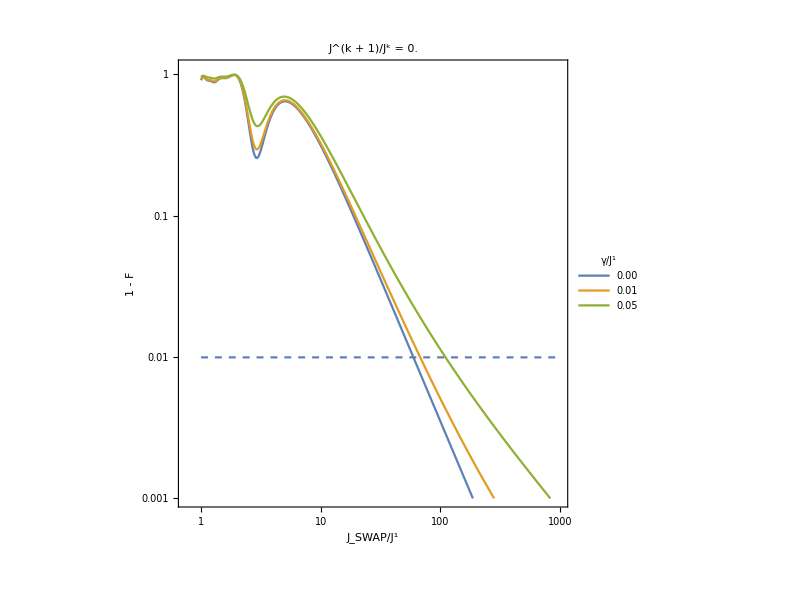
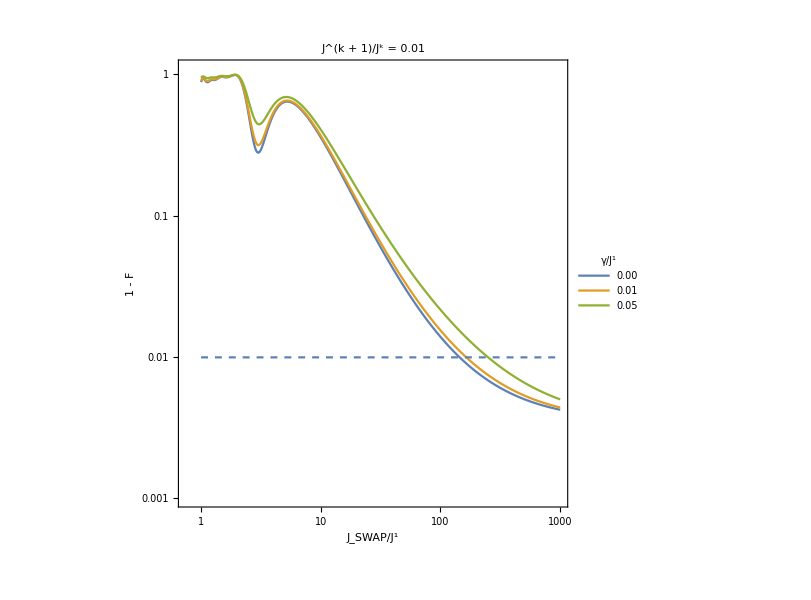
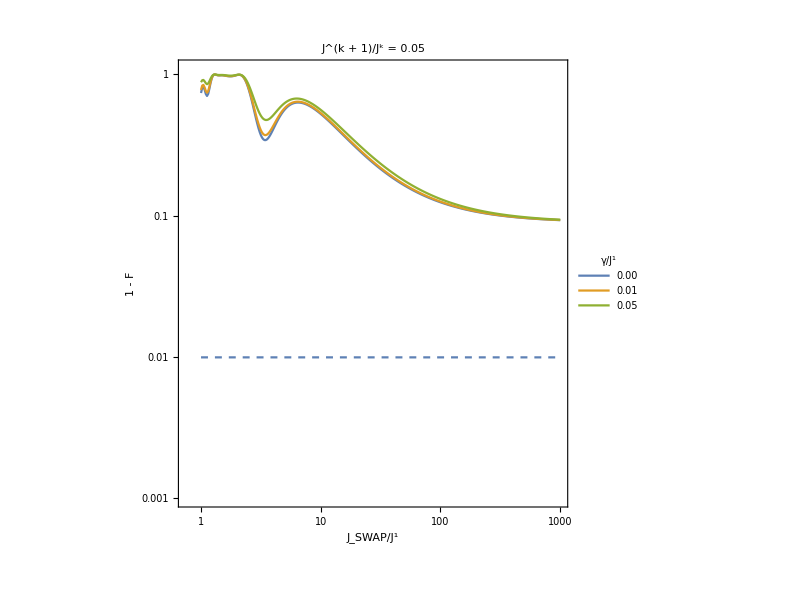

```mathematica
SetDirectory[NotebookDirectory[]];
plotlist=Table[
plotdata = {};
plots = {};
stringσJs = {};
Do[
leng = l;
singlet = sing;
β = beta;
β2= beta;
σJ = 0.0;
σγ = 0.0;
στ = 0.0;
spacing = If[σJ == 0, 0.01, 0.02];
nReals=10000;
nRealsPrime= If[σJ == 0, 0,nReals];
disGam=dg;
filename = "jdata/"<>ToString[leng]<>"_"<>If[singlet,"s","up"]<>"_β"<>StringPadRight[ToString[β2],4,"0"]<>"_γ"<>StringPadRight[ToString[disGam],4,"0"]<>"_"<>"σJ"<>StringPadRight[ToString[N[σJ]],4,"0"]<>"_"<>"σγ"<>StringPadRight[ToString[N[σγ]],4,"0"]<>"_"<>"στ"<>StringPadRight[ToString[N[στ]],4,"0"]<>"_"<>StringPadLeft[ToString[nRealsPrime],5,"0"]<>"_"<>ToString[spacing]<>".m";
If[FileExistsQ[filename],
	AppendTo[stringσJs,StringPadRight[ToString[dg],4,"0"]];
	data = Import[filename];
	AppendTo[plotdata,data];
]

,{l,{6}},{dg,{0.0,0.01,0.05}},{sing,{False}}];

ECThreshold=1-0.999^(2(leng-1));
NicholF=1-0.9^(2(leng-1));
PettaF=1-0.84^(2(leng-1));
Show[ListLogLogPlot[plotdata,Joined->True,AspectRatio->1,ImageSize->600,Frame->True,LabelStyle->20,FrameLabel->{"J_SWAP/J^1","1 - F"},PlotRange->{10*^-4,1.1},PlotLabel->(*"L = "<>ToString[length]<>".*)"   J^(k + 1)/J^k = "<>ToString[β],PlotLegends->LineLegend[Automatic, stringσJs, LegendFunction -> Framed, LegendLabel -> "γ/J^1",LabelStyle->20]],LogLogPlot[{(*PettaF,NicholF,*)ECThreshold},{x,1,1000},PlotStyle->Dashed]]
,{beta,{0.00,0.01,0.05}}];
finalplot = Row[plotlist]
```

## Let’s look at noise

## J Noise

jdata/TEST_4_up_β0.01_γ0.00_σJ0.00_σγ0.00_στ0.00_00000_0.01.m

jdata/TEST_4_up_β0.01_γ0.00_σJ0.01_σγ0.00_στ0.00_00100_0.03.m

jdata/TEST_6_up_β0.01_γ0.00_σJ0.00_σγ0.00_στ0.00_00000_0.01.m

jdata/TEST_6_up_β0.01_γ0.00_σJ0.01_σγ0.00_στ0.00_00100_0.03.m

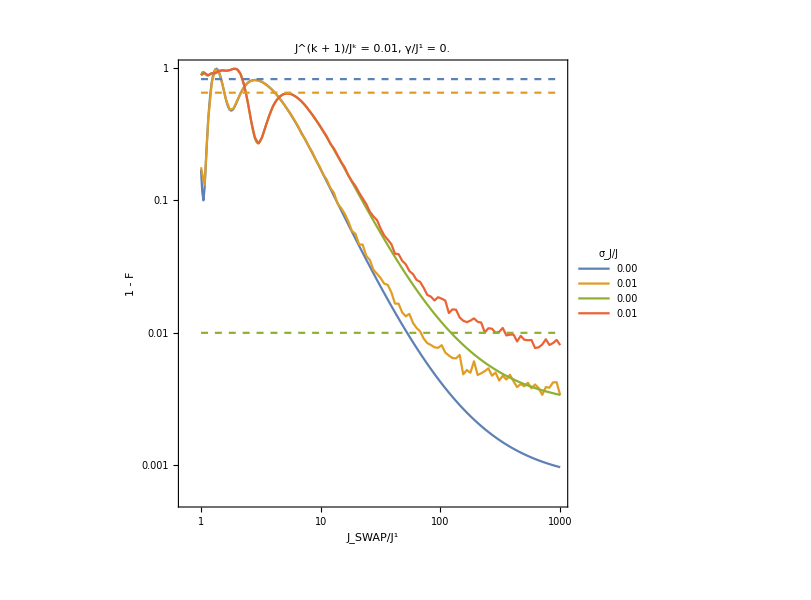

```mathematica
SetDirectory[NotebookDirectory[]];
plotdata = {};
plots = {};
stringσJs = {};
Do[
leng = l;
singlet = sing;
β = beta;
β2= beta;
σJ = sig;
σγ = 0.0;
στ = 0.0;
spacing = If[σJ == 0, 0.01, 0.03];
nReals=100;
nRealsPrime= If[σJ == 0, 0,nReals];
disGam=dg;
filename = "jdata/"<>ToString[leng]<>"_"<>If[singlet,"s","up"]<>"_β"<>StringPadRight[ToString[β2],4,"0"]<>"_γ"<>StringPadRight[ToString[disGam],4,"0"]<>"_"<>"σJ"<>StringPadRight[ToString[N[σJ]],4,"0"]<>"_"<>"σγ"<>StringPadRight[ToString[N[σγ]],4,"0"]<>"_"<>"στ"<>StringPadRight[ToString[N[στ]],4,"0"]<>"_"<>StringPadLeft[ToString[nRealsPrime],5,"0"]<>"_"<>ToString[spacing]<>".m";
Print[filename];
If[FileExistsQ[filename],
	AppendTo[stringσJs,StringPadRight[ToString[sig],4,"0"]];
	data = Import[filename];
	AppendTo[plotdata,data];
]

,{l,{4,6}},{beta,{0.01}},{dg,{0.00}},{sig,{0.0,0.01}},{sing,{False}}];

ECThreshold=1-0.999^(2(leng-1));
NicholF=1-0.9^(2(leng-1));
PettaF=1-0.84^(2(leng-1));
Show[ListLogLogPlot[plotdata,Joined->True,AspectRatio->1,ImageSize->600,Frame->True,LabelStyle->20,FrameLabel->{"J_SWAP/J^1","1 - F"},PlotLabel->(*"L = "<>ToString[length]<>".*)"   J^(k + 1)/J^k = "<>ToString[β]<>", γ/J^1 = "<>ToString[disGam],PlotLegends->LineLegend[Automatic, stringσJs, LegendFunction -> Framed, LegendLabel -> "σ_J/J",LabelStyle->20]],LogLogPlot[{PettaF,NicholF,ECThreshold},{x,1,1000},PlotStyle->Dashed]]
```

## γ Noise

jdata/4_up_β0.00_γ0.10_σJ0.00_σγ0.00_στ0.00_00000_0.01.m

jdata/4_up_β0.00_γ0.10_σJ0.00_σγ0.07_στ0.00_00100_0.01.m

jdata/4_up_β0.00_γ0.10_σJ0.00_σγ0.10_στ0.00_00100_0.01.m

jdata/4_up_β0.00_γ0.10_σJ0.00_σγ0.20_στ0.00_00100_0.01.m

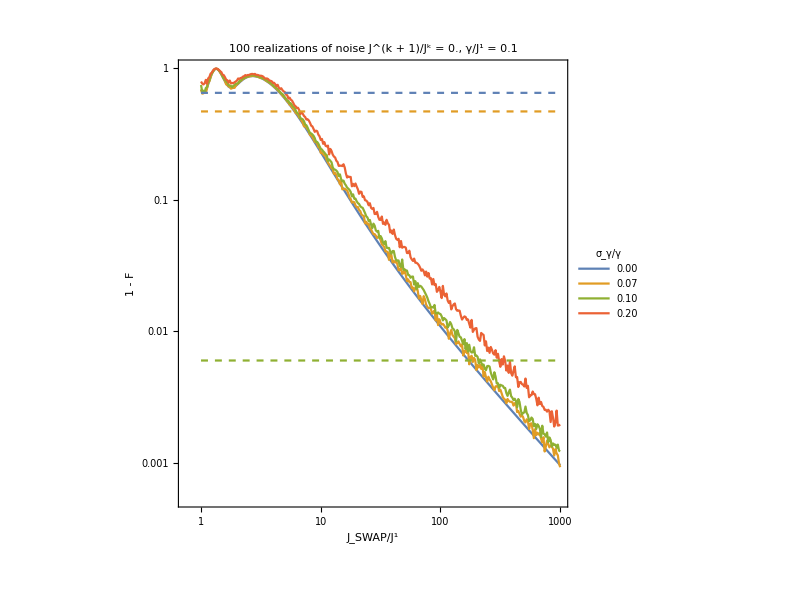

```mathematica
SetDirectory[NotebookDirectory[]];
plotdata = {};
plots = {};
stringσJs = {};
Do[
leng = l;
singlet = sing;
β = beta;
β2= beta;
σJ = 0.0;
σγ = sig;
στ = 0.0;
nReals=100;
spacing = If[Max[σJ,σγ,στ]==0||nReals<=100, 0.01, 0.03];
nRealsPrime= If[Max[σJ,σγ,στ]==0, 0,nReals];
disGam=dg;
filename = "jdata/"<>ToString[leng]<>"_"<>If[singlet,"s","up"]<>"_β"<>StringPadRight[ToString[β2],4,"0"]<>"_γ"<>StringPadRight[ToString[disGam],4,"0"]<>"_"<>"σJ"<>StringPadRight[ToString[N[σJ]],4,"0"]<>"_"<>"σγ"<>StringPadRight[ToString[N[σγ]],4,"0"]<>"_"<>"στ"<>StringPadRight[ToString[N[στ]],4,"0"]<>"_"<>StringPadLeft[ToString[nRealsPrime],5,"0"]<>"_"<>ToString[spacing]<>".m";
Print[filename];
If[FileExistsQ[filename],
	AppendTo[stringσJs,StringPadRight[ToString[sig],4,"0"]];
	data = Import[filename];
	AppendTo[plotdata,data];
]

,{l,{4}},{beta,{0.00}},{dg,{0.10}},{sig,{0.0,0.07,0.1,0.2}},{sing,{False}}];

ECThreshold=1-0.999^(2(leng-1));
NicholF=1-0.9^(2(leng-1));
PettaF=1-0.84^(2(leng-1));
plot=Show[ListLogLogPlot[plotdata,Joined->True,AspectRatio->1,ImageSize->600,Frame->True,LabelStyle->20,FrameLabel->{"J_SWAP/J^1","1 - F"},PlotLabel->(*"L = "<>ToString[length]<>".*)ToString[nReals]<>" realizations of noise   J^(k + 1)/J^k = "<>ToString[β]<>", γ/J^1 = "<>ToString[disGam],PlotLegends->LineLegend[Automatic, stringσJs, LegendFunction -> Framed, LegendLabel -> "σ_γ/γ",LabelStyle->20]],LogLogPlot[{PettaF,NicholF,ECThreshold},{x,1,1000},PlotStyle->Dashed]]
```

General::munfl: Exp[-9799.43] is too small to represent as a normalized machine number; precision may be lost.

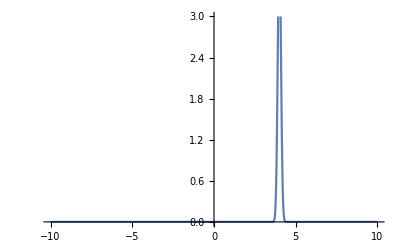

General::munfl: Exp[-9799.43] is too small to represent as a normalized machine number; precision may be lost.

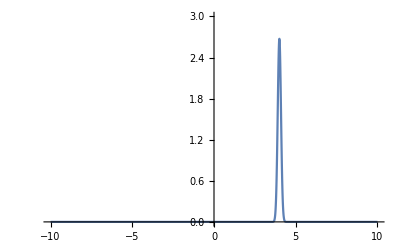

4.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {8.16907×10^224}. NIntegrate obtained 8.58263912306054×10^27949 and 8.58263912306054×10^27949 for the integral and error estimates.

8.58263912306054×10^27949

```mathematica
Clear[myFunc];
myNormal[x_,x0_,σ_]:=Sqrt[1/(2 Pi σ^2)] Exp[-(x-x0)^2/(2 σ^2)]
myDist[x_] := myNormal[x,4,0.1]
myFunc[x_] := Exp[-0.1x]
Plot[myDist[x],{x,-10,10},PlotRange->{0,3}]
Plot[myFunc[x]*myDist[x],{x,-10,10},PlotRange->{0,3}]
myAverage[normal_]:= NIntegrate[x normal[x],{x,-Infinity,Infinity}]
myNewAverage[func_,normal_]:= NIntegrate[func[normal[x]],{x,-Infinity,Infinity}]
myAverage[myDist]
myNewAverage[myFunc,myDist]
```

## τ noise

jdata/4_up_β0.00_γ0.00_σJ0.00_σγ0.00_στ0.00_00000_0.01.m

jdata/4_up_β0.00_γ0.00_σJ0.00_σγ0.00_στ0.05_10000_0.03.m

jdata/4_up_β0.00_γ0.00_σJ0.00_σγ0.00_στ0.10_10000_0.03.m

jdata/4_up_β0.00_γ0.00_σJ0.00_σγ0.00_στ0.20_10000_0.03.m

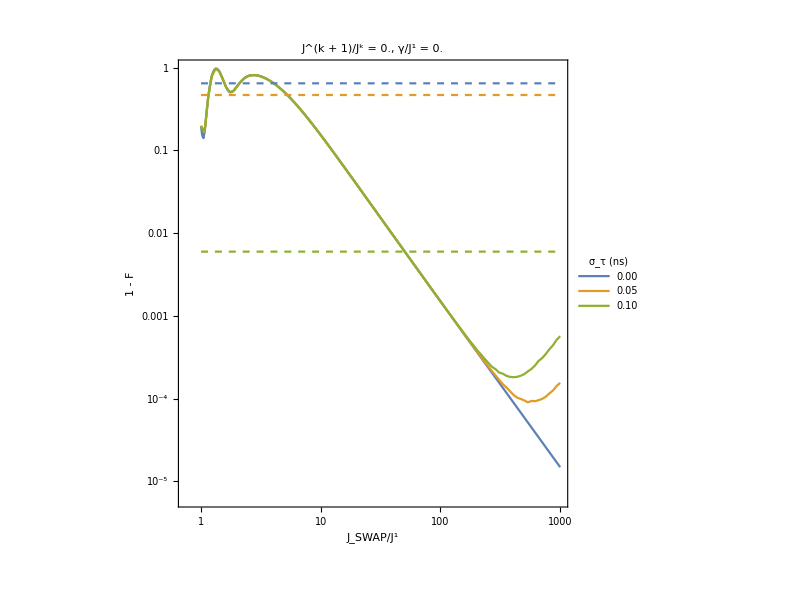

```mathematica
SetDirectory[NotebookDirectory[]];
plotdata = {};
plots = {};
stringσJs = {};
Do[
leng = l;
singlet = sing;
β = beta;
β2= beta;
σJ = 0.0;
σγ = 0.0;
στ = sig;
spacing = If[Max[σJ,σγ,στ]==0, 0.01, 0.03];
nReals=10000;
nRealsPrime= If[Max[σJ,σγ,στ]==0, 0,nReals];
disGam=dg;
filename = "jdata/"<>ToString[leng]<>"_"<>If[singlet,"s","up"]<>"_β"<>StringPadRight[ToString[β2],4,"0"]<>"_γ"<>StringPadRight[ToString[disGam],4,"0"]<>"_"<>"σJ"<>StringPadRight[ToString[N[σJ]],4,"0"]<>"_"<>"σγ"<>StringPadRight[ToString[N[σγ]],4,"0"]<>"_"<>"στ"<>StringPadRight[ToString[N[στ]],4,"0"]<>"_"<>StringPadLeft[ToString[nRealsPrime],5,"0"]<>"_"<>ToString[spacing]<>".m";
Print[filename];
If[FileExistsQ[filename],
	AppendTo[stringσJs,StringPadRight[ToString[sig],4,"0"]];
	data = Import[filename];
	AppendTo[plotdata,data];
]

,{l,{4}},{beta,{0.00}},{dg,{0.0}},{sig,{0.0,0.05,0.1,0.2}},{sing,{False}}];

ECThreshold=1-0.999^(2(leng-1));
NicholF=1-0.9^(2(leng-1));
PettaF=1-0.84^(2(leng-1));
Show[ListLogLogPlot[plotdata,Joined->True,AspectRatio->1,ImageSize->600,Frame->True,LabelStyle->20,FrameLabel->{"J_SWAP/J^1","1 - F"},PlotLabel->(*"L = "<>ToString[length]<>".*)"   J^(k + 1)/J^k = "<>ToString[β]<>", γ/J^1 = "<>ToString[disGam],PlotLegends->LineLegend[Automatic, stringσJs, LegendFunction -> Framed, LegendLabel -> "σ_τ (ns)",LabelStyle->20]],LogLogPlot[{PettaF,NicholF,ECThreshold},{x,1,1000},PlotStyle->Dashed]]
```

## Different levels of noise for L=4, β=0.01

jdata/4_up_0.01_0.00_σ=0.00_00000_0.01.m

jdata/4_up_0.01_0.00_σ=0.01_10000_0.02.m

jdata/4_up_0.01_0.00_σ=0.02_10000_0.02.m

jdata/4_up_0.01_0.00_σ=0.03_10000_0.02.m

jdata/4_up_0.01_0.00_σ=0.04_10000_0.02.m

jdata/4_up_0.01_0.00_σ=0.05_10000_0.02.m

jdata/4_up_0.01_0.00_σ=0.10_10000_0.02.m

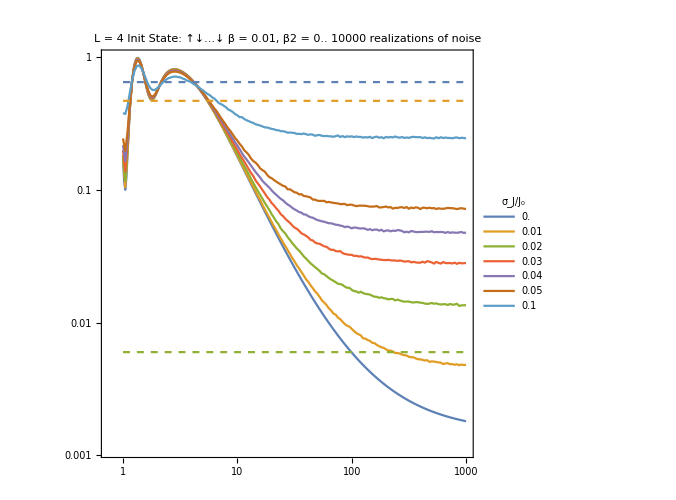

```mathematica
GAMMA = 6.796381511118120480641144794583*10^-5;
SetDirectory[NotebookDirectory[]];
allTogether = True;
plotdata = {};
plots = {};
stringσJs = {};
Do[
length = l;
singlet = sing;
β = beta;
γ0 = If[β==0,0,GAMMA];
σJ = sigma;
spacing = If[sigma == 0, 0.01, 0.02];
disGam = 0.0;
nReals=10000;
nRealsPrime= If[σJ == 0, 0,nReals];
filename = "jdata/"<>ToString[length]<>"_"<>If[singlet,"s","up"]<>"_"<>StringPadRight[ToString[β],4,"0"]<>"_"<>StringPadRight[ToString[disGam],4,"0"]<>"_"<>"σ="<>StringPadRight[ToString[N[σJ]],4,"0"]<>"_"<>StringPadLeft[ToString[nRealsPrime],5,"0"]<>"_"<>ToString[spacing]<>".m";
Print[filename];
If[FileExistsQ[filename],
	AppendTo[stringσJs,ToString[sigma]];
	data = Import[filename];
	If[allTogether,
		AppendTo[plotdata,data];
	,
		AppendTo[plots,ListLogLogPlot[data,Joined->True,AspectRatio->1,ImageSize->Medium,Frame->True,PlotLabel->"L = "<>ToString[length]<>", β = "<>ToString[β]<>", β2="<>ToString[β20],PlotRange->{0,1}]]
	]
]

,{l,{4}},{beta,{0.01}},{sigma,{0.0,0.01,0.02,0.03,0.04,0.05,0.1}},{sing,{False}}];

ECThreshold=1-0.999^(2(leng-1));
NicholF=1-0.9^(2(leng-1));
PettaF=1-0.84^(2(leng-1));
If[allTogether,
	Show[ListLogLogPlot[plotdata,Joined->True,AspectRatio->1,ImageSize->500,Frame->True,PlotLabel->"L = "<>ToString[length]<>" Init State: "<>If[singlet,"S⊗↓↓...↓","↑↓...↓"]<>" β = "<>ToString[β]<>", β2 = "<>ToString[β2]<>". "<>ToString[nReals]<>" realizations of noise",PlotLegends->LineLegend[Automatic, stringσJs, LegendFunction -> Framed, LegendLabel -> "σ_J/J_0"]],LogLogPlot[{PettaF,NicholF,ECThreshold},{x,1,1000},PlotStyle->Dashed]]
,
	Row[plots,Spacer[110]]
]
```

```mathematica
?Grid
```

## Turn everything on!

jdata/4_up_β0.01_γ0.10_σJ0.03_σγ0.20_στ0.05_10000_0.03.m

True

jdata/4_up_β0.01_γ0.10_σJ0.03_σγ0.20_στ0.10_10000_0.03.m

True

jdata/4_up_β0.01_γ0.10_σJ0.03_σγ0.20_στ0.20_10000_0.03.m

True

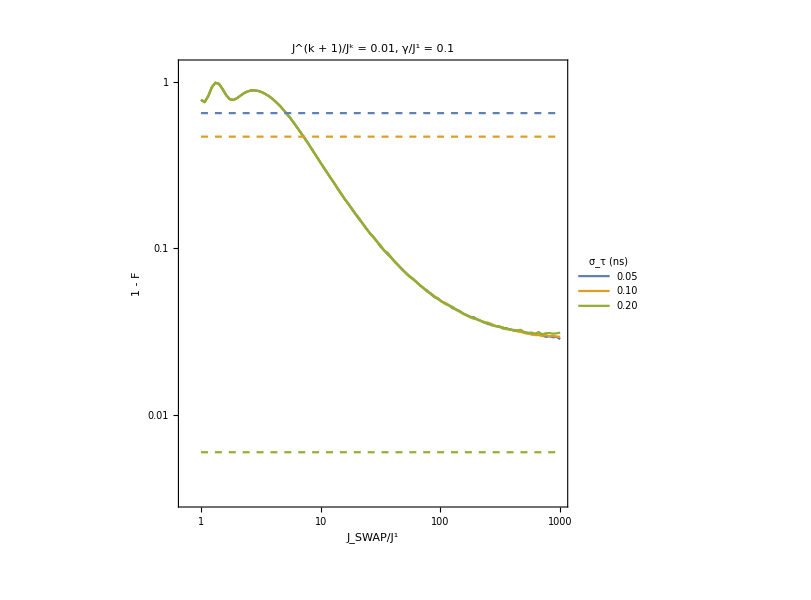

```mathematica
SetDirectory[NotebookDirectory[]];
plotdata = {};
plots = {};
stringσJs = {};
Do[
leng = l;
singlet = sing;
β = beta;
β2= beta;
σJ = 0.03;
σγ = 0.2;
στ = sig;
spacing = If[Max[σJ,σγ,στ]==0, 0.01, 0.03];
nReals=10000;
nRealsPrime= If[Max[σJ,σγ,στ]==0, 0,nReals];
disGam=dg;
filename = "jdata/"<>ToString[leng]<>"_"<>If[singlet,"s","up"]<>"_β"<>StringPadRight[ToString[β2],4,"0"]<>"_γ"<>StringPadRight[ToString[disGam],4,"0"]<>"_"<>"σJ"<>StringPadRight[ToString[N[σJ]],4,"0"]<>"_"<>"σγ"<>StringPadRight[ToString[N[σγ]],4,"0"]<>"_"<>"στ"<>StringPadRight[ToString[N[στ]],4,"0"]<>"_"<>StringPadLeft[ToString[nRealsPrime],5,"0"]<>"_"<>ToString[spacing]<>".m";
Print[filename];
Print[FileExistsQ[filename]];
If[FileExistsQ[filename],
	AppendTo[stringσJs,StringPadRight[ToString[sig],4,"0"]];
	data = Import[filename];
	AppendTo[plotdata,data];
]

,{l,{4}},{beta,{0.01}},{dg,{0.1}},{sig,{0.05,0.1,0.2}},{sing,{False}}];

ECThreshold=1-0.999^(2(leng-1));
NicholF=1-0.9^(2(leng-1));
PettaF=1-0.84^(2(leng-1));
Show[ListLogLogPlot[plotdata,Joined->True,AspectRatio->1,ImageSize->600,Frame->True,LabelStyle->20,FrameLabel->{"J_SWAP/J^1","1 - F"},PlotRange->{10^-2.5,1.2},PlotLabel->(*"L = "<>ToString[length]<>".*)"   J^(k + 1)/J^k = "<>ToString[β]<>", γ/J^1 = "<>ToString[disGam],PlotLegends->LineLegend[Automatic, stringσJs, LegendFunction -> Framed, LegendLabel -> "σ_τ (ns)",LabelStyle->20]],LogLogPlot[{PettaF,NicholF,ECThreshold},{x,1,1000},PlotStyle->Dashed]]
```